Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

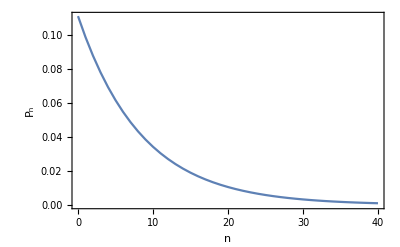

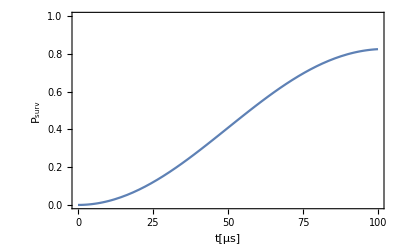

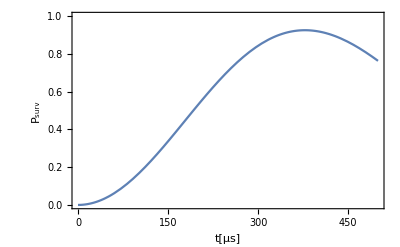

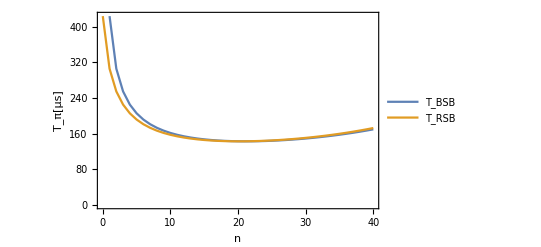

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
SetOptions[{ListPlot,Plot,ErrorListPlot},Frame->True,Axes->False,LabelStyle->Directive[Large],PlotRange->All];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;λ=852nm;(*raman w/l*)
ω=2π 27kHz;(*trap freq*)
θ=.67 ArcTan[10/11]; (*angle in rad b/t 2 axial raman beams*) (*recalibrated based on 9/28 msmt to give 150 us sb pi time at 3.7 nbar and 50us carrier pi time*)
z0=√(ℏ/(2 mCs ω));ηR=0.2;.18;Δk z0;ηOP=k0 z0;k0=(2π)/λ;
Δk=k0 Sin[θ];(*assuming the F3 beam has exactly 0 axial component*)√(2 k0^2(1-Cos[θ]))Sin[(π-θ)/2]; (*general expr*)
ampF4=0.203/√2;
ampF3=.194/√2;
ΩR =π/(83us);2π (√(ampF4 ampF3))/(.19)11.5kHz; (*for 120us ground state sideband pi time; amps = 0.22*)
nbar=8;.094;.15;8;3.7;(*I know this from RNR msmts*)
nbarRSB=.3; 8;.15;.094;3.7;
pCutoff=.001;
μ[m_,n_,η_]:=Exp[-η^2/2] √((nMin!)/(nMax!))η^(nMax-nMin)LaguerreL[nMin,nMax-nMin,η^2]/.nMin->Min[m,n]/.nMax->Max[m,n];
(*thermal occupation probabilities*)
P[n_,nbar_]:= nbar^n/(1+nbar)^(n+1);

SBs[n_]:=Cases[Table[{n+order,μ[n,n+order,ηOP]^2},{order,-4,4}],x_/;Head[x[[2]]]==Real]; (*only keep real results (ie ignore n<0 etc)*)

nCutoff=Ceiling[n/.Solve[P[n,nbar]==pCutoff][[1,1]]];(*go until occupation prob drops to .001*)

Ωc[n_]:=ΩR μ[n,n,ηR];
Ωsb[m_,n_]:=ΩR μ[m,n,ηR];

occ=Table[{n,P[n,nbar]},{n,0,nCutoff}];

flop=Sum[P[n,nbar]/2(1-Cos[Ωc[n]t us]),{n,0,nCutoff}];
flopRSB=Sum[P[n,nbarRSB]/2(1-Cos[Ωsb[n,n+1]t us]),{n,0,nCutoff-1}];
tRSBpi=Table[{n,π/Ωsb[n,n+1]/us},{n,0,40}];
tBSBpi=Table[{n,π/Ωsb[n,n-1]/us},{n,1,40}];
ListPlot[occ,Joined->True,Axes->False,Frame->True,FrameLabel->{"n","P_n","thermal occupation @ <n>="<>ToString[nbar]},LabelStyle->Directive[Large]]
Plot[flop,{t,0,100},PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"t[μs]","P_surv","carrier rabi flop, nbar="<>ToString[nbar]},LabelStyle->Directive[Large]]
Plot[flopRSB,{t,0,500},PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"t[μs]","P_surv","RSB rabi flop, nbar="<>ToString[nbarRSB]},LabelStyle->Directive[Large]]

ListPlot[{tBSBpi,tRSBpi},Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"n","T_π[μs]","sideband pi times"},LabelStyle->Directive[Large],PlotLegends->LineLegend[{"T_BSB","T_RSB"}]]
```

## for given raman pulse length, 1st order cooling sideband transition probability vs n.

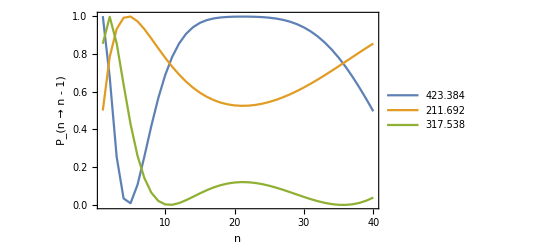

```mathematica
pulsesequence={tBSBpi[[1,2]],tBSBpi[[1,2]]/2,3tBSBpi[[1,2]]/4};
P10=Table[{n,(1-Cos[Ωsb[n,n-1]# us])/2},{n,1,nCutoff}]&/@pulsesequence;(*prob of each vibrational level to go down*)
ListPlot[P10,Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"n","P_(n  →  n - 1)"},LabelStyle->Directive[Large],PlotLegends->LineLegend[pulsesequence]]
```

# optimize pulse sequence

```mathematica
(*initialize; ONLY RUN ONCE*)
Clear[tBSBpi,occtemp];
nPhotons=2 .565; (*number of OP kicks per raman cooling step*)
(*This includes OP from cooling other axes. This script is a little conservative (ie gives more heating than actual) because the OP step redistributes the population that underwent a raman transition, nPhotons times. In reality, only the first optical pumping step applies to this population. The next OP steps apply to the portion that was raman cooled along the other axes, which may be very small if it's the late in the sequence. *)
Pscale=.4; (*height of RSB at coldest*)
occ2=occ[[;;,2]];
nPulsesdone=0;
pulseSeq={};
nEnd=5nbar;
pCutoff=.003;.001;
```

## repeat from here

5/5

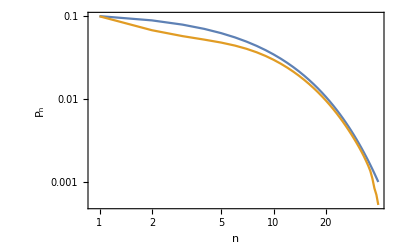

(nbar | nPulsesdone | n|P_n<pCutoff
6.53 | 5 | 30)

{185,203,229,275,381}

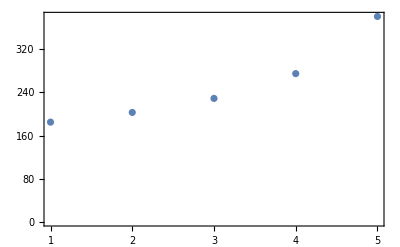

```mathematica
(*do nEnd= 40,30,15,10,5, etc.... script automatically appends sweeps... choose nEnd based on Pn<pcutoff.*)

nRepeat=1;
scaleT=.9; (*nominally 1*)
fixSweepRange=True;(*if you want to use fixed sweep range (over n's)*)
hardcodePulseSeq=False;(*if you want to use the pre determined pulse sequence*)
Do[(*repeat nRepeat times*)
If[fixSweepRange,
nEnd=5;
];
(*calculate pi times for the n's*)
pitimes=Round[scaleT t]/.Flatten@Solve[Ωsb[#,#-1]t us ==π,t]&/@Range[1,nEnd,1]; 
(*to get pi times for 12 kHz instead of 9kHz say, scale t by 9/12 *)
tBSBpi=Reverse[pitimes];

If[hardcodePulseSeq,
tBSBpi={129,126,123,120,118,115,113,111,109,107,105,104,103,101,100,99,98,97,97,96,96,96,95,96,96,96,97,98,100,101,104,107,110,115,121,129,141,159,190,263,129,126,123,120,118,115,113,111,109,107,105,104,103,101,100,99,98,97,97,96,96,96,95,96,96,96,97,98,100,101,104,107,110,115,121,129,141,159,190,263,96,96,95,96,96,96,97,98,100,101,104,107,110,115,121,129,141,159,190,263}; 
];
AppendTo[pulseSeq,tBSBpi];
pulseSeq=Flatten[pulseSeq];
Pdown[n_,t_]:=Pscale(1-Cos[Ωsb[n,n-1]t us])/2;

For[j=1,j≤Length[tBSBpi],j++,
occtemp=occ2;
(*----------------------------raman bsb pulse----------------------------------*)
pdown=Table[Pdown[i,tBSBpi[[j]]],{i,1,Length[occ2]-1}];(*calculate for levels n=1...nCutoff*)
transfer=pdown occtemp[[2;;]]; (*popn transferred down*)(*apply to levels n=1...nCutoff*)
shiftdown=Join[transfer,{0}]; (*fraction added*) 
delete=Join[{0},-transfer]; (*fraction vacated*)

(*----------------------------optical pumping----------------------------------*)
(*ONLY APPLY TO THE POPULATION THAT SUCCESSFULLY UNDERGOES RAMAN TRANSITION, IE, SHIFTDOWN*)
(*effectively optical pumping redistributes shiftdown among motional states.*)
extraOP=Boole[RandomReal[]<nPhotons-Floor[nPhotons]];
(*accounts for fractional probability of scattering a photon*)
Do[(*loop over number of photon scatters per OP step*)
occtemp2=0shiftdown; (*clear temporary register*)
Do[(*loop over all n*)
Do[(*loop over all i in SB[n]*)
If[i+1≤Length[shiftdown],
(*i,n+1 is because i=1 is for n=0*)
occtemp2[[i+1]]+=shiftdown[[n+1]]Cases[SBs[n],x_/;x[[1]]==i][[1,2]]
]
,{i,SBs[n][[;;,1]]}];
,{n,0,Length[shiftdown]-1}];
shiftdown=occtemp2;
(*----------------------------now add everything together----------------------------------*)
occ2=occtemp+shiftdown+delete;
,{jj,Floor[nPhotons]+extraOP}];
If[IntegerQ[j/5],
Print[ToString[j]<>"/"<>ToString[Length[tBSBpi]]]
];
nPulsesdone+=1;
];
occFinal=Thread[{occ[[;;,1]],occ2}];
nEnd=Cases[#-{0,pCutoff}&/@occFinal,x_/;x[[2]]<0][[1,1]];
Print[ListLogLogPlot[{occ,occFinal,{{nEnd,pCutoff}}},PlotRange->{All,{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{"n","P_n"},LabelStyle->Directive[Large]]];
Print[MatrixForm[{{"nbar","nPulsesdone","n|P_n<pCutoff"},
{Round[occ2.occ[[;;,1]],.01],
nPulsesdone,
nEnd}}]];
Print[pulseSeq],
{i,nRepeat}];
ListPlot[pulseSeq]
```

## generate pulse seq. nEnd = 40,30,15,10,5 +6 for each repeat. =130 total

```mathematica
pulseSeq={};
nEnds={40,30,15,10,5};
nEnd=40;
nList=Range[1,nEnd,1];
pitimes=Round[scaleT t]/.Flatten@Solve[Ωsb[#,#-1]t us ==π,t]&/@nList;
pitimes=Thread[{nList,pitimes}];

τ=170;(*measured in "tblackman units" ie, /2.79*)
a=Exp[-#/τ]&/@pitimes[[;;,2]];
nreps=Floor[Max[a]/a]; (*normalize probability to highest prob in the sweep.*)
```

9

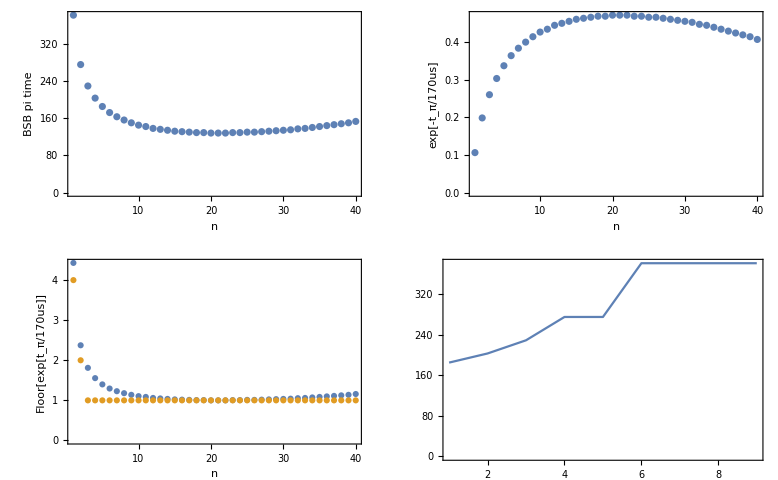

{185,203,229,275,275,381,381,381,381}

{40,30,15,10,5,5}

```mathematica
nEnd2=5;

tBSBpi=Reverse[Flatten[ConstantArray[#[[1]],#[[2]]]&/@Thread[{pitimes[[;;nEnd2,2]],nreps[[;;nEnd2]]}]]];
AppendTo[pulseSeq,tBSBpi];
AppendTo[nEnds,nEnd2];

nEnds=Flatten[nEnds];
pulseSeq=Flatten[pulseSeq];
Length[%]

GraphicsGrid[{{
ListPlot[pitimes,Axes->False,Frame->True,FrameLabel->{"n","BSB pi time"},LabelStyle->Large,PlotRange->All],
ListPlot[a,PlotRange->All,FrameLabel->{"n","exp[-t_π/"<>ToString[τ]<>"us]"}]},
{ListPlot[{Max[a]/a,nreps},PlotRange->All,FrameLabel->{"n","Floor[exp[t_π/"<>ToString[τ]<>"us]]"}],
ListPlot[pulseSeq,Joined->True]}}]
pulseSeq
nEnds
```